0.419945-0.346348 (0.5+x)+9.56988 (0.5+x)^3

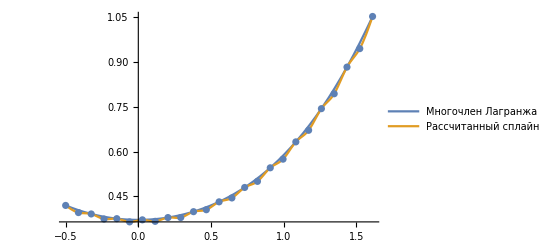

```mathematica
(*Вариант 4*)
(*Задание 2*)
data = {{-0.5,0.419945},{-0.412,0.395988},{-0.324,0.391402},{-0.236,0.374437},{-0.148,0.375642},{-0.06,0.364857},{0.028,0.371704},
{0.116,0.366656},{0.204,0.379343},{0.292,0.379343},{0.38,0.399032},{0.468,0.405545},{0.556,0.43196},{0.644,0.444969},{0.732,0.480039},
{0.82,0.500438},{0.908,0.545871},{0.996,0.574811},{1.084,0.632645},{1.172,0.67142},{1.26,0.743887},{1.348,0.793733},{1.436,0.882993},
{1.524,0.944755},{1.612,1.05247}};
n=Length[data]-1;
step=data[[2,1]]-data[[1,1]];
Array[xdata,n+1,0];Array[ydata,n+1,0];
Array[h,n,0];Array[w,n,0];Array[{p,q,r,b},n,1];
(*Вычисление узлов сплайна*)
For[i=0,i<n+1,i++,
xdata[i]=data[[1,1]]+i*step;
ydata[i]=data[[i+1,2]];];
(*Расчёт коэффициентов сплайна*)
For[i=0,i<n+1,i++,h[i]=xdata[i+1]-xdata[i];
w[i]=ydata[i+1]-ydata[i]];
p[1]=0;r[n]=0;
For[i=1,i<n+1,i++,
p[i]=h[i-1];
r[i]=h[i];
q[i]=2*(h[i]+h[i-1]);
b[i]=3*(w[i]/h[i]-w[i-1]/h[i-1])];
Array[u,n,1];Array[v,n,1];
Array[cs,n,0];
u[1]=(-r[1])/q[1];v[1]=b[1]/q[1];
For[i=2,i<n,i++,s=q[i]+p[i]*u[i-1];
u[i]=-r[i]/s;
v[i]=(b[i]-p[i]*v[i-1])/s];
cs[0]=0;cs[n]=0;
For[i=n-1,i>=1,i--,cs[i]=u[i]*cs[i+1]+v[i]];
(*Расчёт остальных коэффициентов сплайна*)
spln[xdata_,ydata_,cs_,n_,x_]:=
Block[{i=0,h1,a,b,c,d,t},While[x>xdata[i+1],i++];
h1=xdata[i+1]-xdata[i];
a=ydata[i];
b=(ydata[i+1]-ydata[i])/h1-(cs[i+1]+2*cs[i])*h1/3;
c =cs[i];
d=(cs[i+1]-cs[i])/(3*h1);
t=x-xdata[i];
Return[a+b*t+c*t^2+d*t^3]];
sq[x_]:=spln[xdata,ydata,cs,n,x](*Функция сплайна*)
data1=Table[{xdata[i],N[ydata[i]]},{i,0,n}];
f[x_]:=0.371558-5.487052*^-6 x+0.185753 x^2+0.000312 x^3+0.030658 x^4-0.002526 x^5+0.007333 x^6-0.001714 x^7-0.016033 x^8+0.026884 x^9-0.020095 x^10+0.007345 x^11-0.001071 x^12(*используем многочлен Лагранжа 12-й степени, подсчитанный ранее*)
gr3:=Plot[{f[x],sq[x]},{x,xdata[0],xdata[n]},
PlotLegends->{"Многочлен Лагранжа", "Рассчитанный сплайн"}]
gr2:=ListPlot[data1]
sq[x]
Show[{gr3,gr2}]
```